# Multiscale spatiotemporal Lorenz 96 system

#### This Lorenz 96 system has three tiers of nonlinearly interacting variables representing slow/large - scale (X), intermediate (Y), and fast/small - scale (Z) processes . Which AI-based data-driven technique(s) can best predict the spatiotemporal evolution of a multiscale chaotic system, when only the slow/large-scale variables are known (during training) and are of interest (to predict during testing)? We emphasize that, unlike many other studies, our focus is not on reproducing long-term statistics of the underlying dynamical system (al- though that will be examined too) but on predicting the short- term trajectory from a given initial condition.

#### or

#### This set of coupled nonlinear ordinary differential equations (ODEs) is a three-tier extension of Lorenz’s original model (Lorenz, 1996) and has been proposed by Thornes et al. (2017) as a fitting prototype for multiscale chaotic variability of the weather and climate system and a useful test bed for novel methods. In these equations, F = 20 is a large-scale forcing that makes the system highly chaotic, andb=c=e=d=g=10andh=1aretunedtoproduce appropriate spatiotemporal variability of the three variables (see below). The indices are i,j,k = 1,2,...8; thus X has 8 elements while Y and Z have 64 and 512 elements, respectively. In the context of atmospheric circulation, the slow variable X can represent the low-frequency variability of the large-scale circulation, while the intermediate variable Y and fast variable Z can represent synoptic and baroclinic eddies and small- scale convection, respectively.

#### The Lorenz 96 model is a dynamical system formulated by Edward Lorenz in 1996.[1] It is defined as follows. For {\displaystyle i=1,...,N}i=1,...,N: {\displaystyle {\frac {dx_{i}}{dt}}=(x_{i+1}-x_{i-2})x_{i-1}-x_{i}+F}{\displaystyle {\frac {dx_{i}}{dt}}=(x_{i+1}-x_{i-2})x_{i-1}-x_{i}+F} where it is assumed that {\displaystyle x_{-1}=x_{N-1},x_{0}=x_{N}}{\displaystyle x_{-1}=x_{N-1},x_{0}=x_{N}} and {\displaystyle x_{N+1}=x_{1}}{\displaystyle x_{N+1}=x_{1}} and {\displaystyle N\geq 4}{\displaystyle N\geq 4}. Here {\displaystyle x_{i}}x_{i} is the state of the system and {\displaystyle F}F is a forcing constant. {\displaystyle F=8}F=8 is a common value known to cause chaotic behavior.

#### Ed Lorenz was a genius at coming up with simple models that capture the essence of a problem in a much more complex system. His famous butterfly model from 1963 jump-started chaos research, followed by more sophisticated models to describe upscale error growth (1969) and the general circulation of the atmosphere (1984). In 1995, he created another chaotic mode that shall be the topic of this blog post. Confusingly, even though the original paper appeared in 1995, most people refer to the model as the Lorenz 96 (L96) model, which we will also do here.

#### It is is used here to deﬁne 'truth,' i . e . the quantities to be predicted . This system has beenused in several previous studies as a metaphor for the atmosphere (Lorenz 1996; Palmer2001; Smith 2001; Orrell 2002, 2003; Vannitsem and Toth 2002; Roulston and Smith2003),

```mathematica
s = NDSolve[{Derivative[1][x][t] == -3 (x[t] - y[t]), 
    Derivative[1][y][t] == -x[t] z[t] + 26.5 x[t] - y[t], 
    Derivative[1][z][t] == x[t] y[t] - z[t], x[0] == z[0] == 0, 
    y[0] == 1}, {x, y, z}, {t, 0, 400}, MaxSteps -> ∞];
Show[ParametricPlot3D[Evaluate[{x[t], y[t], z[t]} /. s], {t, 0, 400}, 
  PlotPoints -> 1000, 
  PlotStyle -> Directive[Thick, RGBColor[.8, 0, 0]], 
  ColorFunction -> (ColorData["SolarColors", #4] &)], 
 Graphics3D[{ColorData["SolarColors"][0], 
   Sphere[First[({x[t], y[t], z[t]} /. s) /. t -> 0], .75]}], 
 RotationAction -> "Clip", Boxed -> False, SphericalRegion -> False, 
 Axes -> False, ImageSize -> 500]
```

```mathematica
Ω = 
  Polygon[2 {{-Pi, -E}, {0, -1}, {0, 0}, {Pi, 0}, {Pi, E}, {-Pi, 
      E}}];
NDSolve[{Laplacian[
      u[x, y], {x, y}] + λ Cos[v[x, y]]  Sin[u[x, y]] == 0 , 
   Laplacian[
      v[x, y], {x, y}] + λ Sin[u[x, y] ] Sin[v[x, y]] == 0, 
   DirichletCondition[{u[x, y] == 1/10, v[x, y] == 1/20}, 
    True]} /. λ -> 5, {u, 
  v}, {x, y} ∈ Ω]
```

## Base

```mathematica
k=8;
F=10;
c=10;
h=1;
j=32;


step=0.02;
length=200;
toString[i_]:=ToString[If[i==-1,k-1,If[i==0,k,If[i==k+1,1,i]]]];
ClearAll[t]
equation=ToExpression[Join[Table["x"<>ToString[i]<>"'[t]==(x"<>toString[i+1]<>"[t]-x"<>toString[i-2]<>"[t])*x"<>toString[i-1]<>"[t]-x"<>toString[i]<>"[t]+F",{i,k}],
Table["x"<>ToString[i]<>"[0]==RandomReal[10]",{i,k}]]];
var=ToExpression[Table["x"<>ToString[i],{i,k}]];
```

```mathematica
result=NDSolve[equation,var,{t,0,length}];
```

```mathematica
Dimensions[equation]
Dimensions[var]
```

{16}

{8}

```mathematica
value=Table[Evaluate[Map[#[t]&,var]/.result],{t,0,length,step}][[;;,1]];
```

```mathematica
Dimensions[value]
MinMax[value]
```

{10001,8}

{-11.8373,14.845}

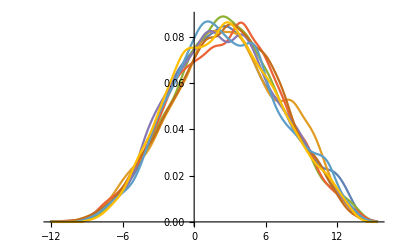

```mathematica
SmoothHistogram[Table[value[[;;,i]],{i,Dimensions[value][[2]]}]]
```

```mathematica
plot=Table[RadialAxisPlot[value[[i]],PlotRange->{-12,12},GridLines->Range[-12,12,4],Axes->Automatic,
	PlotLabel->"t="<>ToString[NumberForm[(i-1)*step,{5,2}]],
	BaseStyle->{FontFamily->"Arial",12}],{i,Length[value]}];
```

```mathematica
Export["/Users/lambda/Documents/NAS/base.gif",plot];
```

## With Y

```mathematica
ClearAll[toString]
```

```mathematica
k=8;
F=10;
c=10;
h=1;
j=32;
b=10;

toStringX[kk_]:=ToString[If[kk==-1,k-1,If[kk==0,k,If[kk==k+1,1,kk]]]];
toStringY[kk_,jj_]:=If[jj<=0,If[kk-1==0,ToString[k],ToString[kk-1]]<>"a"<>ToString[j+jj],
				  If[jj-j>0,If[kk==k,"1",ToString[kk+1]]<>"a"<>ToString[jj-j],
				  ToString[kk]<>"a"<>ToString[jj]]];
```

```mathematica
xequation=ToExpression[Table["x"<>ToString[kk]<>"'[t]==(x"<>toStringX[kk+1]<>"[t]-x"<>toStringX[kk-2]<>"[t])*x"<>toStringX[kk-1]<>"[t]-x"<>toStringX[kk]<>
      "[t]+F-h*c*("<>StringRiffle[Table["y"<>ToString[kk]<>"a"<>ToString[jj],{jj,j}],"[t]+"]<>"[t])/j",{kk,k}]];
```

```mathematica
yequation=ToExpression[Flatten[Table["y"<>toStringY[kk,jj]<>"'[t]==-b*c*y"<>toStringY[kk,jj+1]<>"[t](y"<>toStringY[kk,jj+2]<>"[t]-y"<>toStringY[kk,jj-1]<>
      "[t])-c*y"<>toStringY[kk,jj]<>"[t]+h*c/j*x"<>ToString[kk]<>"[t]",{kk,k},{jj,j}]]];
```

```mathematica
yequation[[31]]
```

y1a31'[t]==(5 x1[t])/16-10 y1a31[t]-100 y1a32[t] (-y1a30[t]+y2a1[t])

```mathematica
xinitial=ToExpression[Table["x"<>ToString[kk]<>"[0]==RandomReal[10]",{kk,k}]];
yinitial=ToExpression[Flatten[Table["y"<>ToString[kk]<>"a"<>ToString[jj]<>"[0]==RandomReal[0]",{kk,k},{jj,j}]]];
```

```mathematica
xvar=ToExpression[Table["x"<>ToString[kk],{kk,k}]];
yvar=ToExpression[Flatten[Table["y"<>ToString[kk]<>"a"<>ToString[jj],{kk,k},{jj,j}]]];
```

```mathematica
result=NDSolve[Join[xequation,yequation,xinitial,yinitial],Join[xvar,yvar],{t,0,length}];
```

```mathematica
base=Table[Evaluate[Map[#[t]&,xvar]/.result],{t,0,length,step}][[;;,1]];
pertubation=Table[Evaluate[Map[#[t]&,yvar]/.result],{t,0,length,step}][[;;,1]];
```

```mathematica
Dimensions[base]
Dimensions[pertubation]
```

{10001,8}

{10001,256}

```mathematica
Table[Mean[Map[Mean,pertubation[[10;;,1+ii*32;;(ii+1)*32]]]],{ii,0,k-1}]
```

{0.056234,0.0571506,0.0599414,0.0603697,0.0609612,0.0575851,0.0585563,0.0640772}

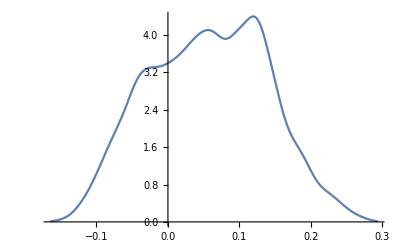
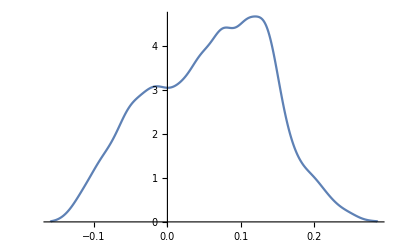
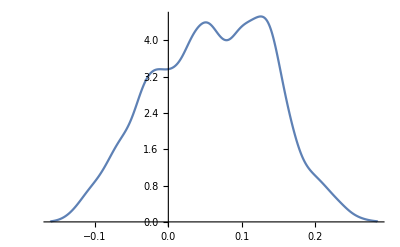
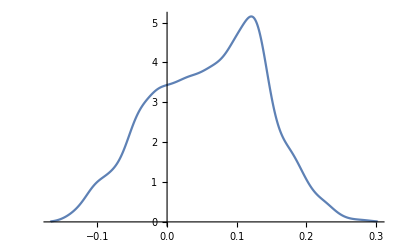
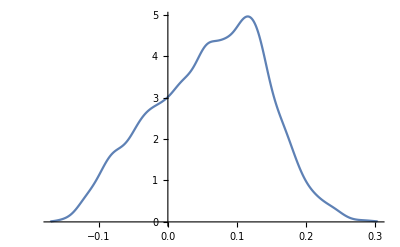
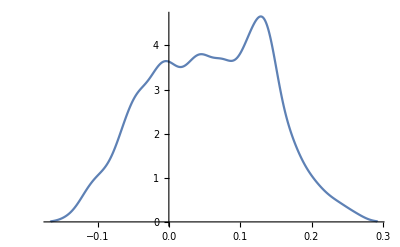
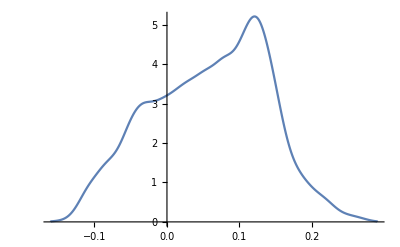
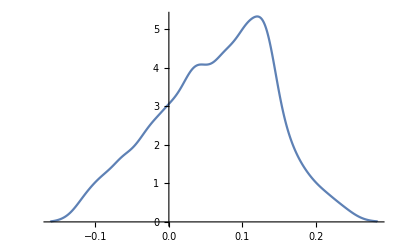

```mathematica
Table[SmoothHistogram[Map[Mean,pertubation[[1;;,1+ii*32;;(ii+1)*32]]]],{ii,0,k-1}]
```

```mathematica
plot=Table[RadialAxisPlot[base[[i]],PlotRange->{-12,12},GridLines->Range[-12,12,4],Axes->Automatic,
	PlotLabel->"t="<>ToString[NumberForm[(i-1)*step,{5,2}]],
	BaseStyle->{FontFamily->"Arial",12}],{i,500}];
```

```mathematica
Export["/Users/lambda/Documents/NAS/pertubation.gif",plot];
```

## Discrimination

#### Single Step

```mathematica
Dimensions[base]
Dimensions[value]
divide={6000,8000};
```

{10001,8}

{10001,8}

```mathematica
(*execute if need normalization*)
base=Block[{mean=Mean[base],var=Sqrt[Variance[base]]},Map[(#-mean)/var&,base]];
value=Block[{mean=Mean[value],var=Sqrt[Variance[value]]},Map[(#-mean)/var&,value]];
```

```mathematica
training=Flatten[Table[{base[[i]]->0,value[[i]]->1},{i,divide[[1]]}]];
validation=Flatten[Table[{base[[i]]->0,value[[i]]->1},{i,divide[[1]],divide[[2]]}]];
test=Flatten[Table[{base[[i]]->0,value[[i]]->1},{i,divide[[2]],Length[base]}]];
```

```mathematica
net=NetChain[{10,BatchNormalizationLayer[],Ramp,DropoutLayer[0.5],
		      10,BatchNormalizationLayer[],Ramp,DropoutLayer[0.5],
		      2,SoftmaxLayer[]},
	"Output"->NetDecoder[{"Class",{0,1}}]]
```

NetChain[<>]

```mathematica
trained=NetTrain[net,RandomSample[training],ValidationSet->validation,MaxTrainingRounds->1000]
```

NetChain[<>]

```mathematica
result=Transpose[{trained[test[[;;,1]]],test[[;;,2]]}];
TableForm[{{Count[result,{0,0}],Count[result,{0,1}]},{Count[result,{1,0}],Count[result,{1,1}]}},
TableAlignments->Center,TableHeadings->{{"TN","FN"}, {"FP","TP"}}]
```

| FP | TP
TN | 1382 | 909
FN | 620 | 1093

#### Double Step

```mathematica
st=3;
training=Flatten[Table[{base[[i;;i+st]]->0,value[[i;;i+st]]->1},{i,divide[[1]]}]];
validation=Flatten[Table[{base[[i;;i+st]]->0,value[[i;;i+st]]->1},{i,divide[[1]],divide[[2]]}]];
test=Flatten[Table[{base[[i;;i+st]]->0,value[[i;;i+st]]->1},{i,divide[[2]],Length[base]-st}]];
```

```mathematica
net=NetChain[{50,BatchNormalizationLayer[],Ramp,DropoutLayer[0.3],
		      50,BatchNormalizationLayer[],Ramp,DropoutLayer[0.3],
		      50,BatchNormalizationLayer[],Ramp,DropoutLayer[0.3],
		      2,BatchNormalizationLayer[],SoftmaxLayer[]},
	"Output"->NetDecoder[{"Class",{0,1}}]]
```

NetChain[<>]

```mathematica
trained=NetTrain[net,RandomSample[training],ValidationSet->validation,MaxTrainingRounds->5000]
```

NetChain[<>]

```mathematica
result=Transpose[{trained[test[[;;,1]]],test[[;;,2]]}];
evaluate={{Count[result,{0,0}],Count[result,{0,1}]},{Count[result,{1,0}],Count[result,{1,1}]}}
```

{{1663,736},{336,1263}}

```mathematica
tt=0
Export["/Users/lambda/Documents/NAS/discriminative_skill_k_"<>ToString[k]<>"_t_"<>ToString[tt]<>".mx",final];
```

0

```mathematica
"/Users/lambda/Documents/NAS/discriminative_skill_k_"<>ToString[k]<>"_t_"<>ToString[tt]<>".mx"
```

/Users/lambda/Documents/NAS/discriminative_skill_k_8_t_0.mx

```mathematica
Table[
If[Not[FileExistsQ["/Users/lambda/Documents/NAS/discriminative_skill_k_"<>ToString[k]<>"_t_"<>ToString[tt]<>".mx"]],
Block[{tempt},
tempt=Table[Block[{training,validation,test,net,trained,result,evaluate},
training=Flatten[Table[{base[[i;;i+st]]->0,value[[i;;i+st]]->1},{i,divide[[1]]}]];
validation=Flatten[Table[{base[[i;;i+st]]->0,value[[i;;i+st]]->1},{i,divide[[1]],divide[[2]]}]];
test=Flatten[Table[{base[[i;;i+st]]->0,value[[i;;i+st]]->1},{i,divide[[2]],Length[base]-st}]];
net=NetChain[{50,BatchNormalizationLayer[],Ramp,DropoutLayer[0.3],
		      50,BatchNormalizationLayer[],Ramp,DropoutLayer[0.3],
		      50,BatchNormalizationLayer[],Ramp,DropoutLayer[0.3],
		      2,BatchNormalizationLayer[],SoftmaxLayer[]},
	"Output"->NetDecoder[{"Class",{0,1}}]];
trained=NetTrain[net,RandomSample[training],ValidationSet->validation,MaxTrainingRounds->2000];
result=Transpose[{trained[test[[;;,1]]],test[[;;,2]]}];
evaluate={{Count[result,{0,0}],Count[result,{0,1}]},{Count[result,{1,0}],Count[result,{1,1}]}};
Print[{tt,st}];
Print[evaluate];
evaluate],{st,0,20}];
Export["/Users/lambda/Documents/NAS/discriminative_skill_k_"<>ToString[k]<>"_t_"<>ToString[tt]<>".mx",tempt];]],{tt,0,50}];
```

$Aborted

```mathematica
finals=Table[Import["/Users/lambda/Documents/NAS/discriminative_skill_k_"<>ToString[k]<>"_t_"<>ToString[tt]<>".mx"],{tt,0,4}];
```

```mathematica
finals[[1]]==finals[[2]]
```

True

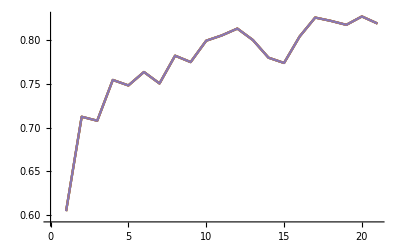

```mathematica
ListLinePlot[Table[(finals[[tt]][[;;,1,1]]+finals[[tt]][[;;,2,2]])/3964.,{tt,5}]]
```